```mathematica
Quit[];
```

## Load the package

```mathematica
<<TRQS`
```

Package TRQS version 0.0.5 (last modification: February 13, 2011).

## Test integer numbers

```mathematica
??TrueRandomInteger
```

TrueRandomInteger[{i_min,i_max}] returns a random integer in the range [i_min,i_max].
TrueRandomInteger[i] returns a random integer in the range [0,i].
TrueRandomInteger[] returns 0 or 1.

TrueRandomInteger[]:=ExternalCall[LinkObject[/home/jam/.Mathematica/Applications/TRQS_Quantis/quantis_random_integer_0,7,7],CallPacket[0,{}]]
 
TrueRandomInteger[{i_Integer,j_Integer}]:=ExternalCall[LinkObject[/home/jam/.Mathematica/Applications/TRQS_Quantis/quantis_random_integer,5,5],CallPacket[0,{i,j}]]
 
TrueRandomInteger[j_Integer]:=ExternalCall[LinkObject[/home/jam/.Mathematica/Applications/TRQS_Quantis/quantis_random_integer_1,6,6],CallPacket[0,{j}]]

```mathematica
{TrueRandomInteger[],TrueRandomInteger[10],TrueRandomInteger[{10,20}]}
```

{0,2,13}

## Test real numbers

```mathematica
??TrueRandomReal
```

TrueRandomReal[{x_min,x_max}] returns a random double in the range [x_min,x_max].
TrueRandomReal[i] returns a random double in the range [0,x].
TrueRandomReal[] returns a random double in the range [0,1].

TrueRandomReal[]:=ExternalCall[LinkObject[/home/jam/.Mathematica/Applications/TRQS_Quantis/quantis_random_double_0,10,10],CallPacket[0,{}]]
 
TrueRandomReal[{x_,y_}]:=ExternalCall[LinkObject[/home/jam/.Mathematica/Applications/TRQS_Quantis/quantis_random_double,8,8],CallPacket[0,{x,y}]]
 
TrueRandomReal[y_]:=ExternalCall[LinkObject[/home/jam/.Mathematica/Applications/TRQS_Quantis/quantis_random_double_1,9,9],CallPacket[0,{y}]]

```mathematica
{TrueRandomReal[],TrueRandomReal[10],TrueRandomReal[{10,20}]}
```

{0.788313,9.67199,19.0885}

## Test the normal distribution

```mathematica
??TrueRandomRealNormal
```

TrueRandomRealNormal[m,s,dims] provides a sample of random numbers distributed according to the normal distribution N[m,s] in an array of dimensions given by dims. Random numbers are obtained using quantum random number generator.

TrueRandomRealNormal[TRQS`Private`m_,TRQS`Private`s_,TRQS`Private`dims_]:=FlattenAt[Fold[Partition[#1,#2]&,TRQS`Private`m+√2 TRQS`Private`s InverseErf[-1+2 Table[TrueRandomReal[],{Times@@TRQS`Private`dims}]],Reverse[TRQS`Private`dims]],1]

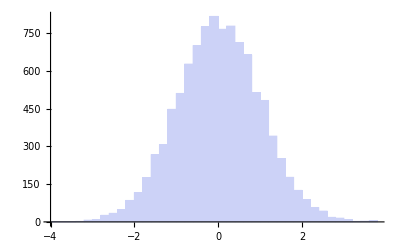

```mathematica
Histogram[Flatten[TrueRandomRealNormal[0,1,{10000}]]]
```

## Test Ginibre matrix

```mathematica
ginibre=Flatten[TrueGinibreMatrix[100,100]];
```

{{-1.71397+0.0187333 ⅈ,0.232751+0.407785 ⅈ,-0.133781+0.797128 ⅈ,0.49623+1.81878 ⅈ},{0.0343377-1.83823 ⅈ,-0.094336+0.490963 ⅈ,0.451447-0.232333 ⅈ,0.849735-1.94803 ⅈ},{-0.0787983-1.21221 ⅈ,1.29433+0.103424 ⅈ,1.4647+0.748995 ⅈ,0.406534+0.196214 ⅈ},{0.378345-1.3079 ⅈ,-1.83048-0.608708 ⅈ,1.70892-4.02376 ⅈ,-0.653781+1.01524 ⅈ}}

## Test random states

```mathematica
statesHS=Table[TrueRandomStateHS[4],{2000}];
```

```mathematica
sortedEvalsHS=Map[Sort[#]&,Map[Chop[Eigenvalues[#]]&,statesHS]]ᵀ;
```

```mathematica
masterplotHS=Histogram[{sortedEvalsHS[[1]],sortedEvalsHS[[2]],sortedEvalsHS[[3]],sortedEvalsHS[[4]]},{0.005},"ProbabilityDensity",PlotRange->{{0,1},{0,61}},ChartBaseStyle->EdgeForm[None],ChartStyle->{Gray,Darker[Gray],LightGray,Darker[LightGray]},
AxesLabel->{"λ","P(λ)"},ImageSize->Large,LabelStyle-> 15];
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/plots"];
```

```mathematica
Export["lambda-prob-hs-trqs.pdf",masterplotHS];
Run[" pdf2ps  -dLanguageLevel=3 lambda-prob-hs-trqs.pdf lambda-prob-hs-trqs.eps"];
```

## Test random states - Bures

```mathematica
statesBures=Table[TrueRandomStateBures[4],{1000}];
```

```mathematica
sortedEvalsBures=Map[Sort[#]&,Map[Chop[Eigenvalues[#]]&,statesBures]]ᵀ;
```

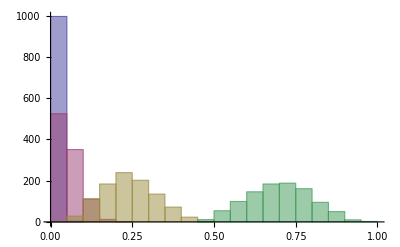

```mathematica
Histogram[{sortedEvalsBures[[1]],sortedEvalsBures[[2]],sortedEvalsBures[[3]],sortedEvalsBures[[4]]}]
```

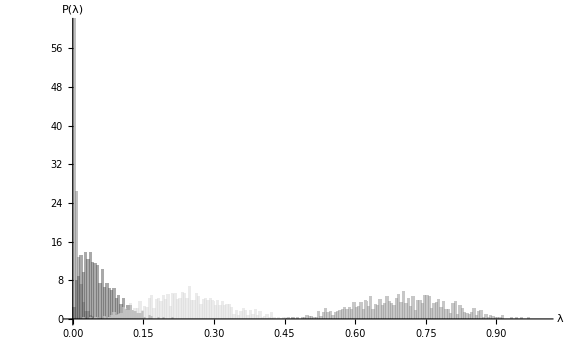

```mathematica
masterplotBures=Histogram[{sortedEvalsBures[[1]],sortedEvalsBures[[2]],sortedEvalsBures[[3]],sortedEvalsBures[[4]]},{0.005},"ProbabilityDensity",PlotRange->{{0,1},{0,61}},ChartBaseStyle->EdgeForm[None],ChartStyle->{Gray,Darker[Gray],LightGray,Darker[LightGray]},
AxesLabel->{"λ","P(λ)"},ImageSize->Large,LabelStyle-> 15]
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/plots"];
```

```mathematica
Export["lambda-prob-bures-trqs.pdf",masterplotBures];
Run[" pdf2ps  -dLanguageLevel=3 lambda-prob-bures-trqs.pdf lambda-prob-bures-trqs.eps"];
```

## Test libQuantis version etc.

```mathematica
QuantisGetLibVersion[]
```

2.5

```mathematica
QuantisGetSerialNumber[]
```

080259A410